# PostProcessing for density jump

Mathematica Notebook created by Andreas Möri on Tueaday 20th April 2020
EPFL ENAC IIC GEL
GC B1 385 (Bâtiment GC)
Station 18, 1015 Lausanne, Switzerland
Phone: +41 (0)21 693 44 70
andreas.mori@epfl.ch
Geo-energy Laboratory EPFL

contributors:
Brice Lecampion  - brice.lecampion@epfl.ch
Carlo Peruzzo - carlo.peruzo@epfl.ch

version n.: 0.0.1

!!IMPORTANT!!!
Before running the script and exploring all functionalities please enter the directory guiding towards your folder with the paclets below in the section “We load the relevant packages” as paclet directory.

## Load data and “Administrative works”

#### Formatting the way of plotting

```mathematica
(*http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html*)
(*ResourceFunction["MaTeXInstall"][];*) (* <-Run  once forevere *) 
Needs["MaTeX`"]
Myfontsize=22;
texStyle={FontFamily->"CMU Serif",FontSize->Myfontsize};
SetOptions[Plot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[LogLogPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListLogPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListLogLinearPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListLogLogPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListVectorPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListLinePlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
```

#### We load the relevant packages

```mathematica
pacletDirectory = StringSplit[NotebookDirectory[],"/examples"][[1]]
PacletDirectoryLoad[pacletDirectory]
```

/Users/amoeri/Documents/Wolfram Mathematica/PyFrac_Mathematica_postprocessing

{/Users/amoeri/Documents/Wolfram Mathematica/PyFrac_Mathematica_postprocessing}

We simply load all the relevant packages. Based on this exercise

```mathematica
<<DescriptionUtilities`
<<NewtonianPulse`
<<RadialScaling`
<<ComputedSolutions`
<<PostProcessRadialPL`
<<RadialPowerLaw`
<<VertexSolutions`
<<rectangularMesh`
```

#### Load the data

Here you load the data of the simulation

```mathematica
dirFiles =NotebookDirectory[]<>"DataStef/" ;(* Points to the folder with the JSon files *)
simulations = {"Mb1e-3_SJ_2o0" ,
"Mb1e-1_DJ_5o0"}(* Name of the simulations *)
For[iter = 1, iter≤ Length[simulations],iter++,
LoadBuoyancyData[simulations[[iter]]]];
Clear[iter]
```

{Mb1e-3_SJ_2o0,Mb1e-1_DJ_5o0}

Now all the data is loaded (We show as an example the properties)
Note: that dl ⧦ the distance to the property change and SJ ⧦ a possible jump in stress and DJ ⧦ a possible jump in the density

```mathematica
Mb1em3SJ2o0prop
Mb1em1DJ5o0prop
```

{KIc→1.3822×10^6,Ep→1.06667×10^9,Cp→0.,Qo→0.05,μp→0.012,Δγ→490.5,sl→{0.,-2.84217×10^-14},dl→400,SJ→2.,DJ→1.}

<|KIc→515228.,Ep→1.06667×10^9,Cp→0.,Qo→0.05,μp→0.012,sl→{7.10543×10^-15,3.55271×10^-15},dl→350,SJ→1.,DJ→5.,Δγ1→490.5,Δγ2→98.1|>

So above you see all properties and the distance to the layer where it happens for both cases

## Post processing examples

#### Track the evolution of the height

We will first track the initial radial evolution based on the radius (half of the height or half of the maximum breadth until deviation from radial)

```mathematica
(* Let us first get the corresponding dimensionless buoyancy of the head and the corresponding Buoyancy lengthscales *)
(* Note: the /.{Δγ-> Δγ1} resp /.{Δγ-> Δγ2} is needed as to chose the correct density contrast. else you get it in function of the density contrast (see first one)*)
ℳ/.vertexScaling["Bh",Mb1em1DJ5o0prop,t]
ℳ/.vertexScaling["Bh",Mb1em1DJ5o0prop,t,False]/.{Δγ-> Δγ1}/.Mb1em1DJ5o0prop
ℳ/.vertexScaling["Bh",Mb1em1DJ5o0prop,t,False]/.{Δγ-> Δγ2}/.Mb1em1DJ5o0prop
```

7.14892×10^-6 Δγ^(2/3)

0.1

0.0341995

Small Exerciseses for you: 
1) find out the Relation between ℳb1 and ℳb2 in function of the density jump DJ.
2) Get Lb1 and Lb2
3) Find out the relation between Lb1 and Lb2 in function of the density jump DJ

The time of deviatio t_b is 96.61 [s]

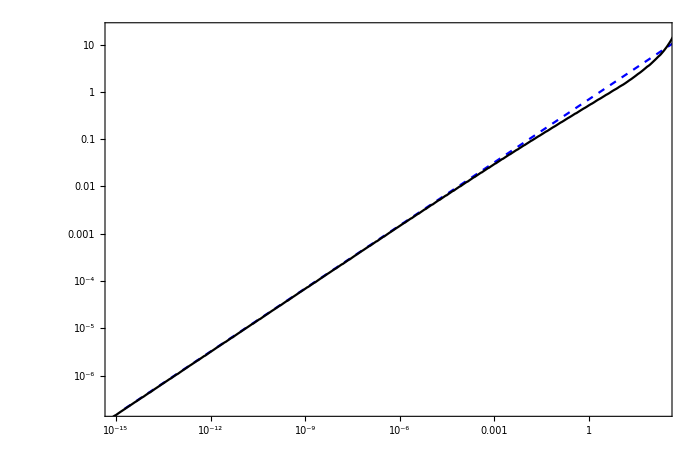

```mathematica
(* We now want to plot the radial evolution up to maybe 2 times t_b *)
(* We first get t_b  (The associate to is used to define which density contrast to use)*)
tb= timeParameters[Merge[{Mb1em1DJ5o0prop,<|Δγ-> Δγ1/.Mb1em1DJ5o0prop|>},Total],False][[-1]];
Print["The time of deviatio t_b is " <> ToString[tb]<>" [s]"]

(* ------ Define some plot options ------ *)
xlabel=MaTeX["t/t_{mk}",FontSize->Myfontsize];
ylabel=MaTeX["L/L_{mk}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio-> 0.65,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

(* ------ Create the figure ------ *)
Show[ListLogLogPlot[Transpose[{Mb1em1DJ5o0["time"]/(timeParameters[Merge[{Mb1em1DJ5o0prop,<|Δγ-> Δγ1/.Mb1em1DJ5o0prop|>},Total],False][[2]]),(FractureLength/.injectionVertexSolutions["M",Mb1em1DJ5o0prop,0.1,Mb1em1DJ5o0["time"],True,False])/(Lstar/.transitionMKScales[Mb1em1DJ5o0prop,False])}],
PlotStyle->{Blue,Dashed},PlotRange->{{Mb1em1DJ5o0["time"][[1]],2 tb},{2 10^-7,20}} ,Joined->True](* This is the blue line, viscosity solution *)
,
ListLogLogPlot[Transpose[{Mb1em1DJ5o0["time"]/(timeParameters[Merge[{Mb1em1DJ5o0prop,<|Δγ-> Δγ1/.Mb1em1DJ5o0prop|>},Total],False][[2]]),(Mb1em1DJ5o0["height"][[1]])/(2 Lstar/.transitionMKScales[Mb1em1DJ5o0prop,False])}],
PlotStyle->{Black},PlotMarkers->None,Joined->True](* This is the black line, simulation *)
,opt]

(* ------ Clear some variables used ------ *)
Clear[tb, xlabel, ylabel, opt]
```

And If we want to plot the full solution of the height for example we do

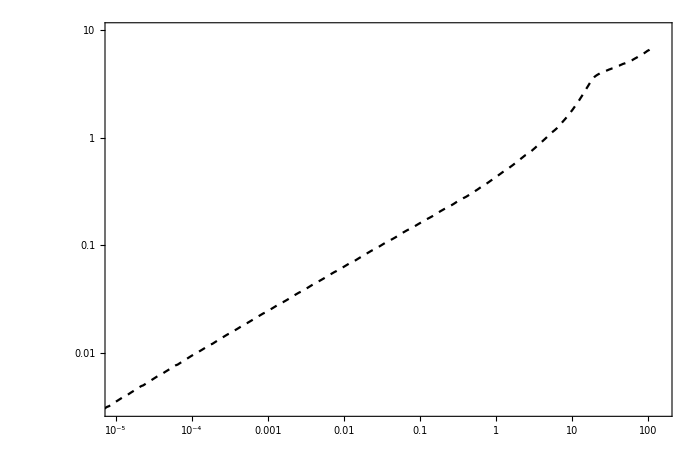

```mathematica
(* ------ Define some plot options ------ *)
xlabel=MaTeX["t/t_{b1}",FontSize->Myfontsize];
ylabel=MaTeX["H/L_{b1}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio-> 0.65,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

(* ------ Create the figure ------ *)
Show[
ListLogLogPlot[Transpose[{Mb1em1DJ5o0["time"]/(timeParameters[Merge[{Mb1em1DJ5o0prop,<|Δγ-> Δγ1/.Mb1em1DJ5o0prop|>},Total],False][[-1]]),(Mb1em1DJ5o0["height"][[1]])/(Lstarh/.vertexScaling["Bh",Mb1em1DJ5o0prop,t,False]/.{Δγ-> Δγ1}/.Mb1em1DJ5o0prop)}],
PlotStyle->{Black,Dashed},PlotMarkers->None,PlotRange->{{10^-5,150},{3 10^-3,10}},Joined->True](* This is the black line, simulation height *)
,opt]
(* ------ Clear some variables used ------ *)
Clear[ xlabel, ylabel, opt]
```

#### Get the prefactor on the breadth

There are two options to get this prefactor. Either by correctly splitting the “max_breadth” value in two: pre and after hitting the density contrast, or by taking the breadth points we exported.

```mathematica
(* ------------- Let's test option one ------------- *)
```

We can split the simulation in a pre and post part according to the height. In fact the height is not direct giving us the distance from the injection point but includes the part of the fracture that did grow towards the bottom. This part is however negligible and we will nonethless use the crieterion H >= dl to get the time when we hit the boundary.

```mathematica
indHit=Position[Mb1em1DJ5o0["height"][[1]],_?(#≥dl/. Mb1em1DJ5o0prop&)][[1,1]]; (* Index where h ≥ dl for the first time *)
(* We can now take the max of the max_breadth in time, or simply the last one for both parts, the result should be the same *)
bmax =Max[Mb1em1DJ5o0["max_breadth"][[1,;;indHit]]]; (* Take the max until then *)
Print["The breadth from the maximum approach is "<>ToString[bmax]<>" [m]"]
Print["The breadth taken when we hit is "<>ToString[Mb1em1DJ5o0["max_breadth"][[1,indHit]]]<>" [m]"];(* Take the max then, to validate *)
(* Then we can get the dimensionles value in this case by normalization *)
𝒷1 = bmax/(Lstarh/.vertexScaling["Bh",Mb1em1DJ5o0prop,t,False]/.{Δγ-> Δγ1}/.Mb1em1DJ5o0prop);
Print["The dimensionless breadth of the lower dike is 𝒷1 = "<>ToString[𝒷1]<>" [-]"]
(* Which we can compare to Möri and Lecampion, (draft). We get*) 
Print["Comparison towards the MöLe draft gives a "<>ToString[Abs[(𝒷1/0.8298259802296755-1)]*100] <>" [%] error."]
```

The breadth from the maximum approach is 88.1216 [m]

The breadth taken when we hit is 88.1216 [m]

The dimensionless breadth of the lower dike is 𝒷1 = 0.85279 [-]

Comparison towards the MöLe draft gives a 2.76733 [%] error.

```mathematica
(* We can now take the max of the max_breadth in time, or simply the last one for both parts, the result should be the same *)
bmax =Max[Mb1em1DJ5o0["max_breadth"][[1,indHit+1;;]]]; (* Take the max from then on then *)
Print["The breadth from the maximum approach is "<>ToString[bmax]<>" [m]"]
Print["The breadth taken when we hit is "<>ToString[Mb1em1DJ5o0["max_breadth"][[1,-1]]]<>" [m]"];(* Take the max then, to validate *)
(* Then we can get the dimensionles value in this case by normalization *)
𝒷2 = bmax/(Lstarh/.vertexScaling["Bh",Mb1em1DJ5o0prop,t,False]/.{Δγ-> Δγ2}/.Mb1em1DJ5o0prop);
Print["The dimensionless breadth of the lower dike is 𝒷2 = "<>ToString[𝒷2]<>" [-]"]
(* Which we can compare to Möri and Lecampion, (draft). We get*) 
Print["Comparison towards the MöLe draft gives a "<>ToString[Abs[(𝒷2/0.7438410389677652-1)]*100] <>" [%] error."]
```

The breadth from the maximum approach is 220.23 [m]

The breadth taken when we hit is 220.23 [m]

The dimensionless breadth of the lower dike is 𝒷2 = 0.728881 [-]

Comparison towards the MöLe draft gives a 2.01113 [%] error.

Note: This approach only works if no overshot is present else anyway there is no stabilized breadth.

Note that in both cases the error is relatively small (even though for the second case we compare a slightly different value of ℳ (0.022 vs 0.034)). We can thus say that it seems (to be checked with further simulations) the stabilized breadth is reached and equal independent of lithology changes below and simply depends on the properties of the actual layer the fracture propagates in.

We visualize this in a next step and use the figure of MöLe for comparison

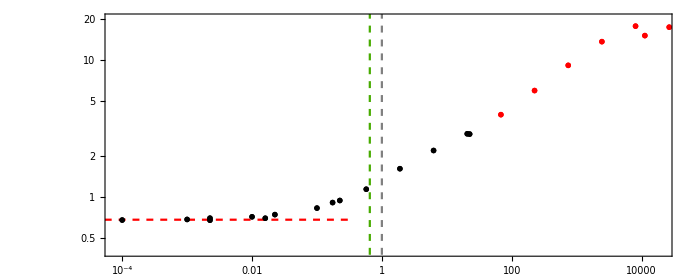
```mathematica
colList = {RGBColor[0.28,0.67,0.],Purple};
points ={{ℳ/.vertexScaling["Bh",Mb1em1DJ5o0prop,t,False]/.{Δγ-> Δγ1}/.Mb1em1DJ5o0prop,𝒷1},{ℳ/.vertexScaling["Bh",Mb1em1DJ5o0prop,t,False]/.{Δγ-> Δγ2}/.Mb1em1DJ5o0prop,𝒷2}};
points={#}&/@points;
Show[-Graphics-,
ListLogLogPlot[points,PlotStyle->colList,PlotMarkers->fm["Diamond",7]]]
```

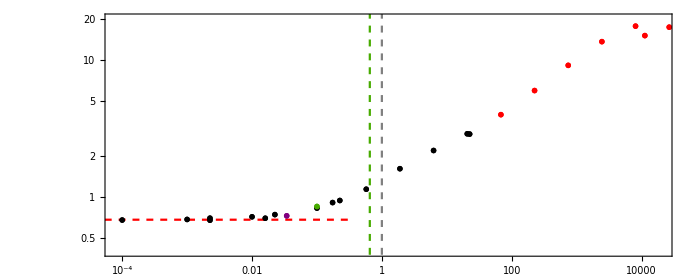

```mathematica
(* ------ Clear some variables used ------ *)
Clear[ bmax, 𝒷1, 𝒷2,colList,points]
```

#### Plot some footprints

We will now show you how to plot a set of footprints  in a colored way

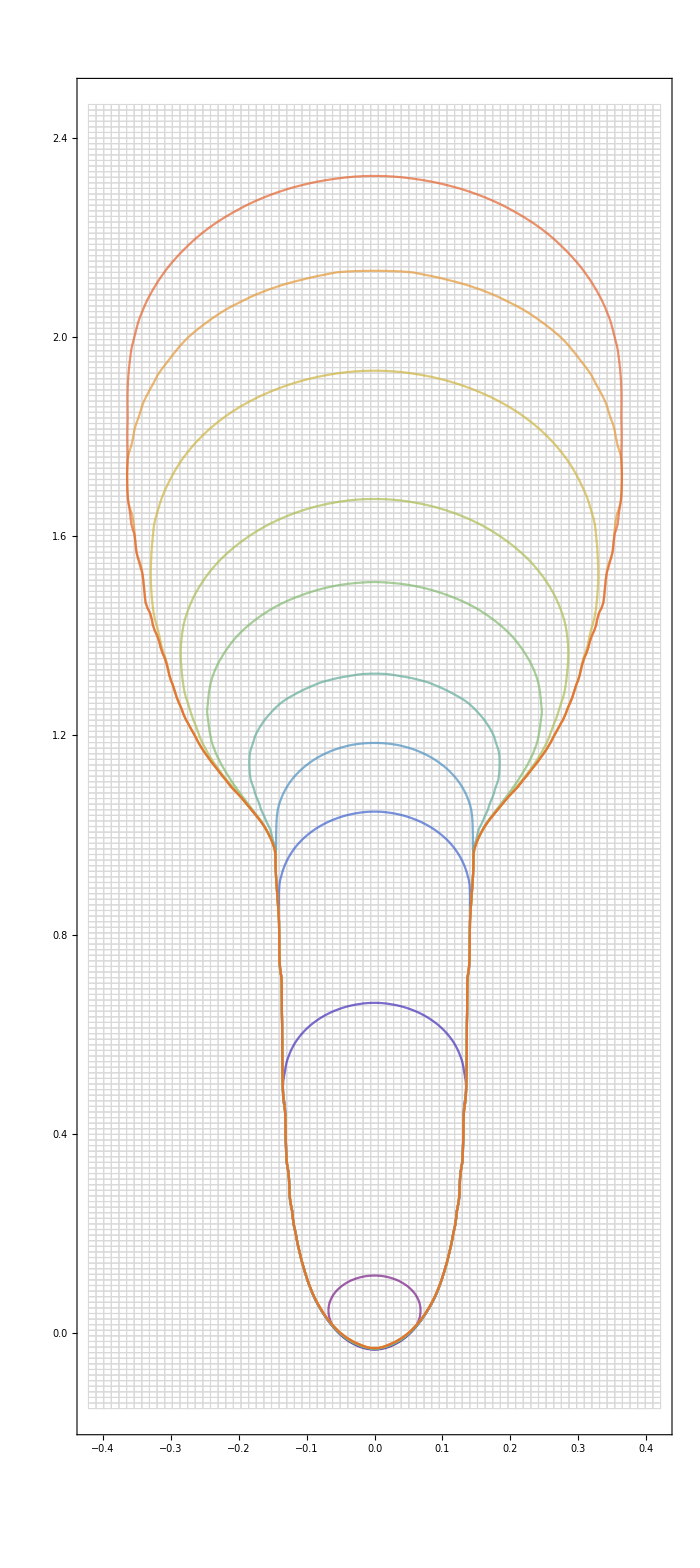

```mathematica
(* Define which layer's properties to use *)
layerIndex = 2;

(* Define if you want to plot in dimensionless form *)
dimless = True;

(* generating the fooprints correctly and getting the background *)
(* Like this
				coloredFootprints[simulations[[2]]] 
the function returns dimensionless coordinates normalized by default by the first layer*)
(* Like this
				coloredFootprints[simulations[[2]],False] 
the function returns dimensional coordinates*)
(* Like this
				coloredFootprints[simulations[[2]],True,layerIndex] 
the function returns dimensionless coordinates normalized by the layer with index layerIndex*)
plotInfos = coloredFootprints[simulations[[2]],dimless,layerIndex];

(* Get the simulation name in the correct way *)
sim=StringReplace[simulations[[2]],"_"->""];
sim =StringReplace[sim,"-"->"m"];
sim =StringReplace[sim,"+"->"p"];

(* We generate the legend and the labels *)
If[dimless,
Δγloc=getΔγ[Symbol[sim<>"prop"],layerIndex];
Legendi=Round[(Symbol[sim<>"fractures"]["time"])/(timeParameters[Merge[{Symbol[sim<>"prop"],<|Δγ-> Δγloc|>},Total],False][[-1]]),0.0001];
xlabel=MaTeX["\\frac{x}{L_{b"<>ToString[layerIndex]<>"}} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{z}{L_{b"<>ToString[layerIndex]<>"}} \\text{ [-]}",FontSize->Myfontsize];
optlegend={PlotLegends->LineLegend["Rainbow",MaTeX`MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\frac{t}{t_{b"<>ToString[layerIndex]<>"}} \\text{ [-]}"},FontSize->Myfontsize]]};
,
Legendi=Round[Symbol[sim<>"fractures"]["time"],0.0001];
xlabel=MaTeX`MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX`MaTeX["z \\text{ [m]}",FontSize->Myfontsize];
optlegend={PlotLegends->LineLegend["Rainbow",MaTeX`MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\text{(time [s])}"},FontSize->Myfontsize]]};
]

opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

(* Plooting the colored footprints *)
Show[("Background"/.plotInfos),ListPlot["Footprints"/.plotInfos,Joined->True,optlegend,PlotStyle->"Style"/.plotInfos],opt]

(* ------ Clear some variables used ------ *)
Clear[ layerIndex, dimless, plotInfos,sim,Δγloc, Δγloc, Legendi,xlabel,ylabel,optlegend, opt]
```

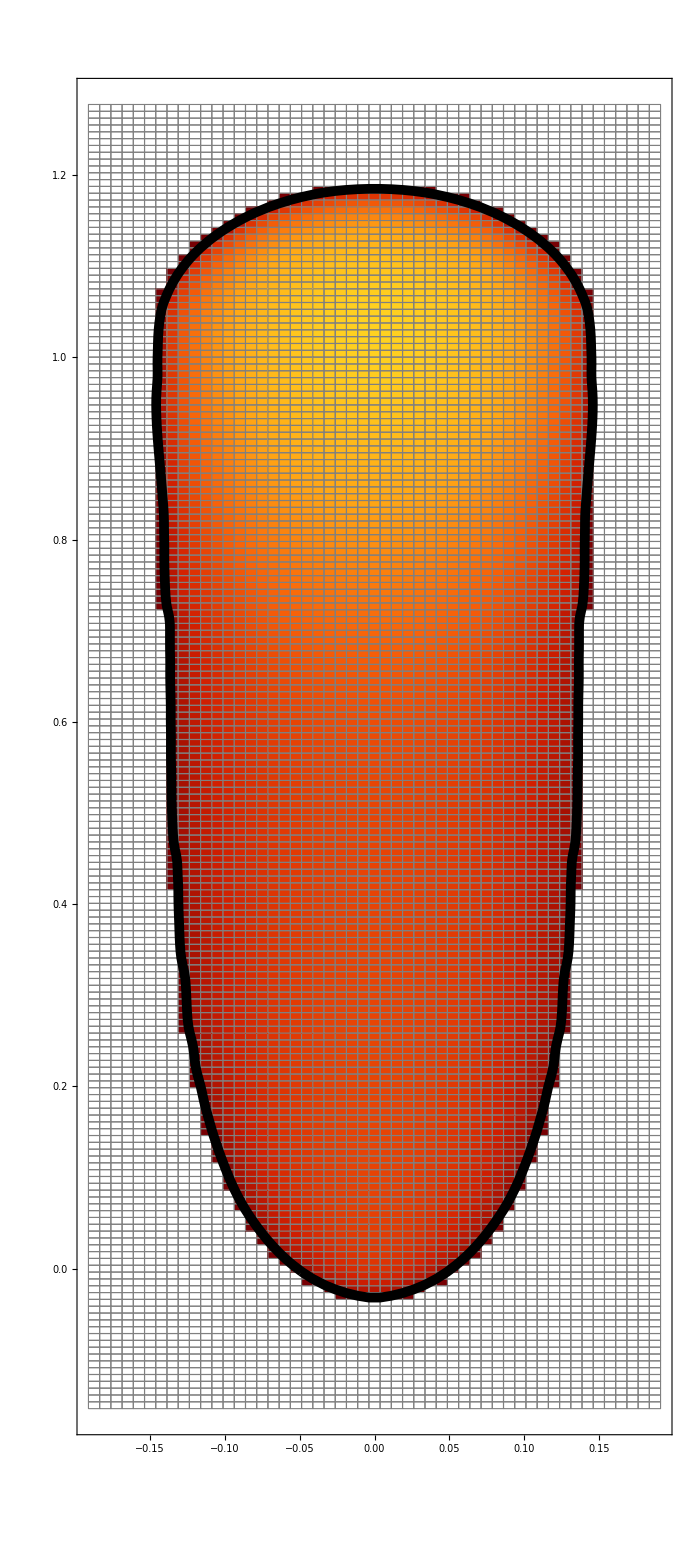

```mathematica
(* Define which layer's properties to use *)
layerIndex = 2;

(* Define if you want to plot in dimensionless form *)
dimless = True;

(* Get the simulation name in the correct way *)
sim=StringReplace[simulations[[2]],"_"->""];
sim =StringReplace[sim,"-"->"m"];
sim =StringReplace[sim,"+"->"p"];

(* generating the footrpint correctly and getting the background *)
index =4;

(* generating the fooprints correctly and getting the background *)
(* Like this
				get2DDistributions[simulations[[2]],index] 
the function returns dimensionless coordinates and dimensionless width all due to the data set of the injeciton layer *)
(* Like this
				get2DDistributions[simulations[[2]],index,False] 
the function returns dimensional coordinates and dimensional width *)
(* Like this
				get2DDistributions[simulations[[2]],index,True,layerIndex] 
the function returns dimensionless coordinates and dimensionless width all due to the data set of the layer Index*)
(* If you want to get the pressure then you need to define it as the last variable and so you need to define all variables
				get2DDistributions[simulations[[2]],index,True,layerIndex,"pn"] 
the function returns dimensionless coordinates and dimensionless pressure all due to the data set of the layer Index*)
plotInfos =get2DDistributions[simulations[[2]],index,dimless,layerIndex];

(* We generate the legend and the labels *)
If[dimless,
Δγloc=getΔγ[Symbol[sim<>"prop"],layerIndex];
fp={(Symbol[sim <>"fractures"]["fp_x"][["Index"/.plotInfos]])/(KIc^(2/3)/Δγ^(2/3)/.Symbol[sim<>"prop"]/.{Δγ-> Δγloc}),(Symbol[sim <>"fractures"]["fp_y"][["Index"/.plotInfos]])/(KIc^(2/3)/Δγ^(2/3)/.Symbol[sim<>"prop"]/.{Δγ-> Δγloc})}ᵀ;
xlabel=MaTeX["\\frac{x}{L_{b"<>ToString[layerIndex]<>"}} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{z}{L_{b"<>ToString[layerIndex]<>"}} \\text{ [-]}",FontSize->Myfontsize];
,
xlabel=MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["z \\text{ [m]}",FontSize->Myfontsize];
fp={Symbol[sim <>"fractures"]["fp_x"][["Index"/.plotInfos]],Symbol[sim <>"fractures"]["fp_y"][["Index"/.plotInfos]]}ᵀ;
];

optlegend={PlotLegends->("Legend"/.plotInfos)};

(* We generate the legend and the labels *)
opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

(* Plooting the colored footprints *)
Show[("Graphics"/.plotInfos),ListPlot[fp,Joined->True,PlotStyle->{Black,Thickness[.01]},optlegend],optlegend,opt]

(* ------ Clear some variables used ------ *)
Clear[ layerIndex, dimless, plotInfos,sim,Δγloc, Δγloc,xlabel,ylabel,optlegend, opt, index, fp]
```

#### Plot a section footprints

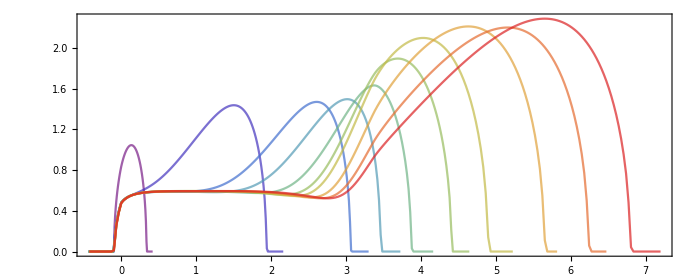

```mathematica
layerIndex = 1;
dimless = True;

(* Get the simulation name in the correct way *)
sim=StringReplace[simulations[[2]],"_"->""];
sim =StringReplace[sim,"-"->"m"];
sim =StringReplace[sim,"+"->"p"];

(* Get the number of sections *)
nSlices =Length["time_list"/.Symbol[sim<>"sections"]["w_vert_slice_"]];

(* Define the style of the sections *)
styling =Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/(Length["time_list"/.Symbol[sim<>"sections"]["w_vert_slice_"]]-1)]};

(* We generate the legend and the labels, and decide on the dimensional or dimensionless part *)
If[dimless,
Δγloc=getΔγ[Symbol[sim<>"prop"],layerIndex];(* Get the according density contrast *)
Legendi=Round[("time_list"/.Symbol[sim<>"sections"]["w_vert_slice_"])/(timeParameters[Merge[{Symbol[sim<>"prop"],<|Δγ-> Δγloc|>},Total],False][[-1]]),0.0001];(* Get the according dimensionless times *)

(* Generate the labels *)
xlabel=MaTeX["\\frac{z}{L_{b"<>ToString[layerIndex]<>"}} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{w}{W_{h"<>ToString[layerIndex]<>"}} \\text{ [-]}",FontSize->Myfontsize];

(* generate the legend *)
optlegend={PlotLegends->LineLegend["Rainbow",MaTeX`MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\frac{t}{t_{b"<>ToString[layerIndex]<>"}} \\text{ [-]}"},FontSize->Myfontsize]]};

(* Get the length and opening scale *)
(* Note the 10^3 is needed because the unit of the extracted opening is [mm] *)
divider = {Lstarh/.vertexScaling["Bh",Merge[{Symbol[sim<>"prop"],<|Δγ-> Δγloc|>},Total],t,False],10^3 wstar/.vertexScaling["Bh",Merge[{Symbol[sim<>"prop"],<|Δγ-> Δγloc|>},Total],t,False]};
,
Legendi=Round[Symbol[sim<>"sections"]["time"],0.0001];(* Get the according times *)

(* Generate the labels *)
xlabel=MaTeX`MaTeX["z \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX`MaTeX["W \\text{ [mm]}",FontSize->Myfontsize];

(* generate the legend *)
optlegend={PlotLegends->LineLegend["Rainbow",MaTeX`MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\text{(time [s])}"},FontSize->Myfontsize]]};

(* No opening and length-scale to be defined *)
divider = {1,1};
];

opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,PlotRange-> All};

openings= ConstantArray[0,{nSlices,1}];

For[iter = 1,iter≤ nSlices,iter++,
openings[[iter]]={(("w_sampling_coords_"<>ToString[iter-1])/.Mb1em1DJ5o0sections["w_vert_slice_"])/divider[[1]],(("w_"<>ToString[iter-1])/.Mb1em1DJ5o0sections["w_vert_slice_"])/divider[[2]]}ᵀ;
];

Show[ListPlot[openings,Joined->True,optlegend,PlotStyle->styling],opt]
```

Another Exercise for you:
Plot the dimensionless pressure of the extracted horizontal section.

## Some specific functions are defined hereafter

Load the buoyant data

```mathematica
LoadBuoyancyData[simName_]:=Module[{sim,props},
(* Put the string in a form that can be used as a symbol by mathematica *)
sim=StringReplace[simName,"_"->""];
sim =StringReplace[sim,"-"->"m"];
sim =StringReplace[sim,"+"->"p"];

(* Check if the symobl already exists else delete it *)
If[ValueQ[Evaluate[Symbol[sim]]],
Clear[Symbol[sim]];];

Evaluate[Symbol[sim]] =Association[Import[dirFiles<>simName<>"_geometrics.json"]]; (* Load geometrical data *)

(* Check if the symobl already exists else delete it *)
If[ValueQ[Evaluate[Symbol[sim<>"prop"]]],
Clear[Symbol[sim<>"prop"]];];

(* Load properties dictionary *)
If[KeyExistsQ[Symbol[sim],"Vo"],
props = {KIc-> √(π/32)Symbol[sim]["Kp"],Ep-> Symbol[sim]["Ep"],Cp-> Symbol[sim]["Cp"],Qo-> Symbol[sim]["Qo"],μp-> Symbol[sim]["mup"],Δγ-> Symbol[sim]["Dgamma"],Vo-> Symbol[sim]["Qo"] * Symbol[sim]["ts"],ts-> Symbol[sim]["ts"],sl-> Symbol[sim]["sources_coordinates"],dl->Symbol[sim]["dlayer"]};,
props = {KIc-> √(π/32)Symbol[sim]["Kp"],Ep-> Symbol[sim]["Ep"],Cp-> Symbol[sim]["Cp"],Qo-> Symbol[sim]["Qo"],μp-> Symbol[sim]["mup"],Δγ-> Symbol[sim]["Dgamma"],sl-> Symbol[sim]["sources_coordinates"],dl->Symbol[sim]["dlayer"]};];

If[KeyExistsQ[Symbol[sim],"SJ"],props=Join[props,{SJ->Symbol[sim]["SJ"]}];,
props=Join[props,{SJ->1.}];];

If[KeyExistsQ[Symbol[sim],"DJ"],props=Join[props,{DJ->Symbol[sim]["DJ"]}];
props =Join[props,{Δγ1-> Δγ/.props,Δγ2-> Δγ /DJ/.props}];
props=KeyDrop[props,Δγ];
Evaluate[Symbol[sim<>"prop"]]=props;
,
Evaluate[Symbol[sim<>"prop"]]=Join[props,{DJ->1.}];];

(* Check if the symobl already exists else delete it *)
If[ValueQ[Evaluate[Symbol[sim<>"fractures"]]],
Clear[Symbol[sim<>"fractures"]];];

(* Load footprints and so on *)
Evaluate[Symbol[sim<>"fractures"]] = Association[Import[dirFiles<>simName<>"_fractures.json"]];

(* Check if the symobl already exists else delete it *)
If[ValueQ[Evaluate[Symbol[sim<>"sections"]]],
Clear[Symbol[sim<>"sections"]];];

(* Load sections *)
Evaluate[Symbol[sim<>"sections"]] = Association[Import[dirFiles<>simName<>"_sections.json"]];

(* Check if the symobl already exists else delete it *)
If[ValueQ[Evaluate[Symbol[sim<>"breadth"]]],
Clear[Symbol[sim<>"breadth"]];];

(* Load breadt *)
Evaluate[Symbol[sim<>"breadthLocal"]] = Association[Import[dirFiles<>simName<>"_breadth.json"]];

];
```

With this function one can plot footprints in different colors

```mathematica
(* Function to get necessary ingredients for colored footprints *)
coloredFootprints[sim_, dimless_:True,dg_:0]:=Module[{Δγloc,LastMesh,stringSim, footprints, styling, bck, divider,iter},

(* Put the string in a form that can be used as a symbol by mathematica *)
stringSim=StringReplace[sim,"_"->""];
stringSim =StringReplace[stringSim,"-"->"m"];
stringSim =StringReplace[stringSim,"+"->"p"];

(* Decide on the delta gamma to use *)
Δγloc=getΔγ[Symbol[stringSim<>"prop"],dg];


(* Decide if to plot in dimensionless form *)
If[dimless ,divider =KIc^(2/3)/Δγ^(2/3)/.Symbol[stringSim<>"prop"]/.{Δγ-> Δγloc};,
divider = 1;];

(* Generate the mesh of the last footprint *)
LastMesh =meshPlan[0,0,0,0,Symbol[stringSim <>"fractures"]["mesh_info"][[-1]]];

(* We need to order the footprints correctly *)
footprints = ConstantArray[0,{Length[Symbol[stringSim <>"fractures"]["time"]],1}];
For[iter = 1,iter≤ Length[Symbol[stringSim <>"fractures"]["time"]],iter ++,
footprints[[iter]]={Symbol[stringSim <>"fractures"]["fp_x"][[iter]],Symbol[stringSim <>"fractures"]["fp_y"][[iter]]}ᵀ/divider;
];

(* Define the style of footprints *)
styling =Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/(Length[Symbol[stringSim <>"fractures"]["time"]]-1)]};

(* Generate the background mesh *)
bck =Graphics[{EdgeForm[{Thin,LightGray}],Transparent,GraphicsComplex[LastMesh["vertexes"]/divider,Polygon[LastMesh["conn"][[1;;]]]]}];

(* Output the style *)
{"Style"-> styling, "Footprints"-> footprints, "Background"-> bck, "LastMesh"-> LastMesh}

];
```

With this function one can Plot opening or pressure distribution within the crack

```mathematica
get2DDistributions[sim_,index_,dimless_:True,dg_:0,var_:"w"]:=Module[{stringSim,Δγloc,ind, theMesh, scale, Cdat, graphics, TheColor, iter, pn, Leg, limits,divider},

(* Put the string in a form that can be used as a symbol by mathematica *)
stringSim=StringReplace[sim,"_"->""];
stringSim =StringReplace[stringSim,"-"->"m"];
stringSim =StringReplace[stringSim,"+"->"p"];

(* Check if the index is ok *)
If[Abs[index]≥ Length[Symbol[stringSim <>"fractures"]["time"]],
ind =Sign[index] Length[Symbol[stringSim <>"fractures"]["time"]];
Print["Index was out of range so limiting index was taken instead"];,
ind = index;
];

(* Decide on the delta gamma to use *)
Δγloc=getΔγ[Symbol[stringSim<>"prop"],dg];

(* Get the corresponding mesh *)
theMesh =rectangularMesh`meshPlan[0,0,0,0,Symbol[stringSim <>"fractures"]["mesh_info"][[ind]]];

If[dimless,
divider = KIc^(2/3)/Δγ^(2/3)/.Symbol[stringSim <>"prop"]/.{Δγ-> Δγloc};
,
divider = 1;
];
(* Load opening or pressure in function of var *)
If[var == "w",
scale =Rescale[Symbol[stringSim <>"fractures"]["w"][[ind]],{Min[Symbol[stringSim <>"fractures"]["w"][[ind]]],Max[Symbol[stringSim <>"fractures"]["w"][[ind]]]}];
limits = {Min[Symbol[stringSim <>"fractures"]["w"][[ind]]],Max[Symbol[stringSim <>"fractures"]["w"][[ind]]]};
,
pn=Symbol[stringSim <>"fractures"]["pn"][[ind]];
pn[[Flatten[Position[Symbol[stringSim <>"fractures"]["pn"][[ind]],_?(#≥ 0.0&)]]]]=0;
scale =Rescale[pn,{Min[pn],Max[pn]}];
limits = {Min[pn],Max[pn]};
];

(* Generate the graphics *)
Cdat =ColorData["SolarColors"]/@scale[[1;;]]; 
graphics =ConstantArray[0,{Length[scale],1}];
For[iter = 1,iter≤ Length[scale],iter++,
If[scale[[iter]] == 0,TheColor=Transparent;,TheColor =Cdat[[iter]];];
graphics[[iter]]=Graphics[{EdgeForm[{Thin,Gray}],TheColor,Polygon[(theMesh["vertexes"][[theMesh["conn"][[iter]]]])/divider]}];
];

(* Generate the legend *)
If[dimless,
If[var ≠ "pn",
Leg =BarLegend[{"SolarColors",limits/(KIc^(4/3)/(Ep Δγ^(1/3))/.Symbol[stringSim <>"prop"]/.{Δγ-> Δγloc})},LegendLayout->"Row",LegendLabel->MaTeX["w/W",FontSize->Myfontsize]];
,
Leg =BarLegend[{"SolarColors",limits/(KIc^(2/3) Δγ^(1/3)/.Symbol[stringSim <>"prop"]/.{Δγ-> Δγloc})},LegendLayout->"Row",LegendLabel->MaTeX["pn/P",FontSize->Myfontsize]];
];
,
If[var ≠ "pn",
Leg =BarLegend[{"SolarColors",limits},LegendLayout->"Row",LegendLabel->MaTeX["w \\text{ [mm]}",FontSize->Myfontsize]];
,
Leg =BarLegend[{"SolarColors",limits 1000},LegendLayout->"Row",LegendLabel->MaTeX["pn \\text{ [MPa]}",FontSize->Myfontsize]];
];
];

(* Output data *)
{"Mesh"-> theMesh,"Scale"-> scale,"Graphics"-> graphics,"Index"-> ind, "Legend"-> Leg}
];
```

Function to check which density contrast to use

```mathematica
getΔγ[props_,dg_]:=Module[{},
If[MemberQ[{1,2},dg],
If[KeyExistsQ[props,Δγ1],
Symbol["Δγ"<>ToString[dg]]/.props,
Print["No simulation with two different density contrasts!"];
Abort[]
],
If[Not[KeyExistsQ[props,Δγ]],
Print["Simulation with different Δγ encountered but no choice provided!"];
Print["As default Δγ1 was used!"];
Δγ1/.props
]
,
Δγ/.props
]
]
```